# Data

## Facts Known About the Project

## Costs & Limits

```mathematica
queryCost=Quantity[0.01,"$"];
elementsPerQuery=100;
maxMatrixRows=25;
maxMatrixCols=25;
elementsPerSecond=1000;
queriesPerSecond=1000;
```

```mathematica
maxQueriesPerDay=1000*60*60*24;
maxElementsPerDay=1000*60*60*24;
```

## Map Specifications

```mathematica
nodesCountTotal=1575357;
nodesCountMain =458121;

edgesCountTotal=1706406;
edgesCountMain=589170;

waysCount=275937;
```

# Speculations

## Cost of Querying the Whole Map

```mathematica
averageDegree=edgesCountMain/nodesCountMain;
numQueriesNeeded=nodesCountMain;
numElementsNeeded=nodesCountMain*averageDegree;
```

```mathematica
price=numQueriesNeeded*queryCost
```

4 581.21 $

# Comparisons

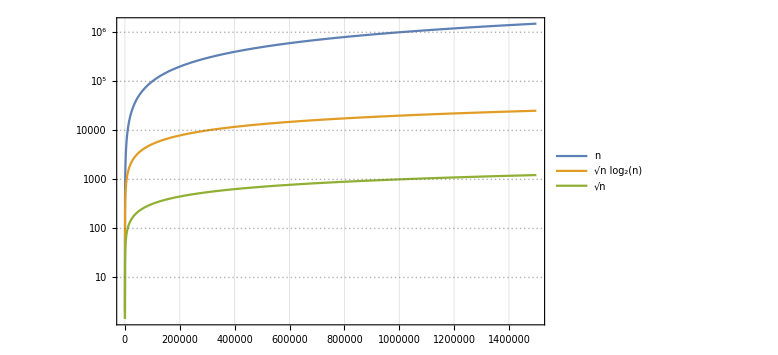

```mathematica
LogPlot[{n,√n Log[2,n],√n},{n,2,1500000},PlotTheme->"Detailed",ImageSize->Large,PlotRange->All]
```

```mathematica
Manipulate[N/@{n,1/2 √n Log[2,n],√n}*queryCost,{n,1,nodesCountMain,1000}]
```